## The RGB Cube corners.

```mathematica
RGBCube = {{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}};
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}}
MatrixForm[RGBCube]
```

{{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}}

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

## Rotation Matrices

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R[α_,β_, γ_]:=RotationMatrixZ[γ].RotationMatrixY[β].RotationMatrixX[α]
```

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
YAB[θ_]:=RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
```

```mathematica
Print[MatrixForm[FullSimplify[YAB[θ]]].MatrixForm[RGBCube],"=",MatrixForm[FullSimplify[YAB[θ]. RGBCube]]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | -Cos[θ]/(√6)+Sin[θ]/(√2)
-Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6)).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
YABCube[θ_]:=FullSimplify[YAB[θ].RGBCube]
```

```mathematica
MatrixForm[YABCube[θ]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
Manipulate[corners = Transpose[YABCube[θ]];Graphics3D[{Polygon[corners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[1]]]]]]],Polygon[corners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[2]]]]]]],Polygon[corners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[3]]]]]]],Polygon[corners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[4]]]]]]],Polygon[corners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[5]]]]]]],Polygon[corners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[6]]]]]]]},Lighting->"Neutral"],{θ,0,Pi}]
```

```mathematica
MatrixForm[{TrigExpand[YABCube[θ +Pi/6][[2]]],YABCube[θ ][[3]]}]
```

(0 | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | -Cos[θ]/(√2)+Sin[θ]/(√6) | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

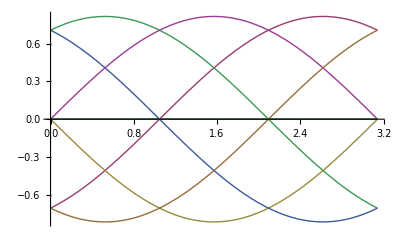

```mathematica
Plot[Evaluate[YABCube[θ][[3]], {θ, 0, Pi}]]
```

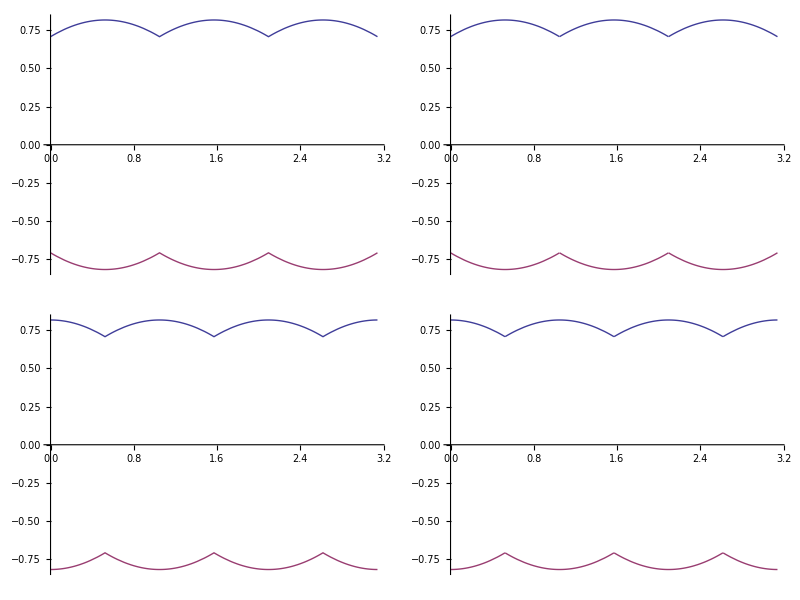

```mathematica
Grid[{{Plot[{Max[YABCube[θ ][[3]]],Min[YABCube[θ ][[3]]]},{θ,0,Pi}], Plot[{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)},{θ,0,Pi}]},{Plot[{Max[YABCube[θ ][[2]]],Min[YABCube[θ ][[2]]]},{θ,0,Pi}],Plot[{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{θ,0,Pi}]}}]
```

```mathematica
YABPolygon[θ_]:=Transpose[{Take[YABCube[θ ][[2]],{2,7}],Take[YABCube[θ ][[3]],{2,7}]}]
```

```mathematica
Manipulate[Graphics[{Black,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[YABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-√(2/3) ,√(2/3) },{-√(2/3) ,√(2/3) }}],{θ,0,Pi}]
```

```mathematica
YABAxisRanges[θ_]:={{0,Sqrt[3]},{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)}};
YABAxisRanges[θ]
```

{{0,√3},{Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6)},{Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)}}

```mathematica
scaleMatrix[θ_] := {{1/(2 YABAxisRanges[θ][[1,2]]),0,0},{0,1/(2 YABAxisRanges[θ][[2,2]]),0},{0,0,1/(2 YABAxisRanges[θ][[3,2]])}};
nYAB[θ_]:=scaleMatrix[θ]. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
MatrixForm[FullSimplify[YAB[θ]]]
MatrixForm[FullSimplify[YAB[θ]. RGBCube]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | -Cos[θ]/(√6)+Sin[θ]/(√2)
-Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6))

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
nYABCube[θ_]:=FullSimplify[nYAB[θ].RGBCube]
```

```mathematica
nYABPolygon[θ_]:=Transpose[{Take[nYABCube[θ ][[2]],{2,7}],Take[nYABCube[θ ][[3]],{2,7}]}]
```

```mathematica
Manipulate[Graphics[{Black,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[nYABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-1/2,1/2},{-1/2 ,1/2}}],{θ,0,Pi}]
```

## Discrete Representation of the rotation

We have a source which makes discrete steps of 1/srcRange the question is to what degree of precision do we need to represent the transformation given that we require a precision of 1/wrkRange. What is required is the smallest number which can result from the transformation of a unit cube!

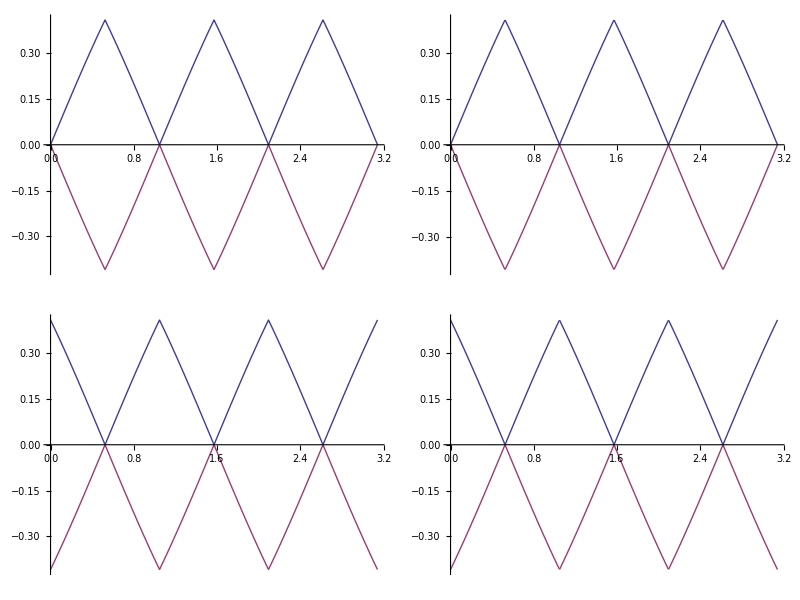

```mathematica
Grid[{{Plot[{Min[Abs[YABCube[θ ][[3,{2,3,4,5,6,7}]]]],-Min[Abs[YABCube[θ ][[3,{2,3,4,5,6,7}]]]]},{θ,0,Pi}], Plot[{√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]]},{θ,0,Pi}]},{Plot[{Min[Abs[YABCube[θ ][[2,{2,3,4,5,6,7}]]]],-Min[Abs[YABCube[θ ][[2,{2,3,4,5,6,7}]]]]},{θ,0,Pi}],Plot[{√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]]},{θ,0,Pi}]}}]
```

```mathematica
Manipulate[{MatrixForm[N[d[YAB[θ],srcRange]]- N[YAB[θ]]],MatrixForm[N[YAB[θ]]]},{θ,0,Pi},{srcRange,1,255,1}]
```

```mathematica
]
```

```mathematica
MatrixForm[YAB[θ]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | -Cos[θ]/(√6)+Sin[θ]/(√2)
-Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6))

```mathematica
d[src_,srcRange_]:=IntegerPart[src*srcRange]/srcRange
```

```mathematica
Manipulate[{MatrixForm[N[d[YAB[θ],tRange].RGBCube]],MatrixForm[N[YAB[θ].RGBCube]]},{{θ,-0.1537},-Pi,Pi},{tRange,1,765,1}]
```

```mathematica
3 255
```

765

```mathematica
FullSimplify[d[d[nYAB[θ],tRange].RGBCube,dstRange]- nYAB[θ].RGBCube]
```

{{0,-1/6+IntegerPart[(dstRange IntegerPart[tRange/6])/tRange]/dstRange,-1/3+IntegerPart[(2 dstRange IntegerPart[tRange/6])/tRange]/dstRange,-1/6+IntegerPart[(dstRange IntegerPart[tRange/6])/tRange]/dstRange,-1/3+IntegerPart[(2 dstRange IntegerPart[tRange/6])/tRange]/dstRange,-1/6+IntegerPart[(dstRange IntegerPart[tRange/6])/tRange]/dstRange,-1/3+IntegerPart[(2 dstRange IntegerPart[tRange/6])/tRange]/dstRange,-1/2+IntegerPart[(3 dstRange IntegerPart[tRange/6])/tRange]/dstRange},{0,IntegerPart[(dstRange IntegerPart[(tRange (√3 Cos[θ]+3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])])/tRange]/dstRange-(√3 Cos[θ]+3 Sin[θ])/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]]),IntegerPart[(dstRange (-IntegerPart[(√3 tRange Cos[θ])/(3 Cos[Mod[π/6+θ,π/3]]+√3 Sin[Mod[π/6+θ,π/3]])]+IntegerPart[(tRange (√3 Cos[θ]+3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])]))/tRange]/dstRange+(√3 Cos[θ]-3 Sin[θ])/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]]),-IntegerPart[(dstRange IntegerPart[(√3 tRange Cos[θ])/(3 Cos[Mod[π/6+θ,π/3]]+√3 Sin[Mod[π/6+θ,π/3]])])/tRange]/dstRange+(√3 Cos[θ])/(3 Cos[Mod[π/6+θ,π/3]]+√3 Sin[Mod[π/6+θ,π/3]]),IntegerPart[(dstRange (-IntegerPart[(√3 tRange Cos[θ])/(3 Cos[Mod[π/6+θ,π/3]]+√3 Sin[Mod[π/6+θ,π/3]])]+IntegerPart[(tRange (√3 Cos[θ]-3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])]))/tRange]/dstRange+(√3 Cos[θ]+3 Sin[θ])/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]]),IntegerPart[(dstRange IntegerPart[(tRange (√3 Cos[θ]-3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])])/tRange]/dstRange+(-√3 Cos[θ]+3 Sin[θ])/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]]),IntegerPart[(dstRange (IntegerPart[(tRange (√3 Cos[θ]-3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])]+IntegerPart[(tRange (√3 Cos[θ]+3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])]))/tRange]/dstRange-(√3 Cos[θ])/(3 Cos[Mod[π/6+θ,π/3]]+√3 Sin[Mod[π/6+θ,π/3]]),1/dstRange IntegerPart[1/tRangedstRange (-IntegerPart[(√3 tRange Cos[θ])/(3 Cos[Mod[π/6+θ,π/3]]+√3 Sin[Mod[π/6+θ,π/3]])]+IntegerPart[(tRange (√3 Cos[θ]-3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])]+IntegerPart[(tRange (√3 Cos[θ]+3 Sin[θ]))/(6 Cos[Mod[π/6+θ,π/3]]+2 √3 Sin[Mod[π/6+θ,π/3]])])]},{0,IntegerPart[(dstRange IntegerPart[(tRange (3 Cos[θ]-√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])])/tRange]/dstRange+(-3 Cos[θ]+√3 Sin[θ])/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]]),IntegerPart[(dstRange (IntegerPart[(√3 tRange Sin[θ])/(3 Cos[Mod[θ,π/3]]+√3 Sin[Mod[θ,π/3]])]+IntegerPart[(tRange (3 Cos[θ]-√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])]))/tRange]/dstRange-(3 Cos[θ]+√3 Sin[θ])/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]]),IntegerPart[(dstRange IntegerPart[(√3 tRange Sin[θ])/(3 Cos[Mod[θ,π/3]]+√3 Sin[Mod[θ,π/3]])])/tRange]/dstRange-(√3 Sin[θ])/(3 Cos[Mod[θ,π/3]]+√3 Sin[Mod[θ,π/3]]),IntegerPart[(dstRange (IntegerPart[(√3 tRange Sin[θ])/(3 Cos[Mod[θ,π/3]]+√3 Sin[Mod[θ,π/3]])]-IntegerPart[(tRange (3 Cos[θ]+√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])]))/tRange]/dstRange+(3 Cos[θ]-√3 Sin[θ])/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]]),-IntegerPart[(dstRange IntegerPart[(tRange (3 Cos[θ]+√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])])/tRange]/dstRange+(3 Cos[θ]+√3 Sin[θ])/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]]),IntegerPart[(dstRange (IntegerPart[(tRange (3 Cos[θ]-√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])]-IntegerPart[(tRange (3 Cos[θ]+√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])]))/tRange]/dstRange+(√3 Sin[θ])/(3 Cos[Mod[θ,π/3]]+√3 Sin[Mod[θ,π/3]]),IntegerPart[(dstRange (IntegerPart[(√3 tRange Sin[θ])/(3 Cos[Mod[θ,π/3]]+√3 Sin[Mod[θ,π/3]])]+IntegerPart[(tRange (3 Cos[θ]-√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])]-IntegerPart[(tRange (3 Cos[θ]+√3 Sin[θ]))/(6 Cos[Mod[θ,π/3]]+2 √3 Sin[Mod[θ,π/3]])]))/tRange]/dstRange}}

```mathematica
Manipulate[cube=d[d[nYAB[θ],tRange].RGBCube- nYAB[θ].RGBCube,dstRange];{MatrixForm[cube  dstRange],Max[cube] dstRange,Min[cube] dstRange},{{θ,-0.1537},-Pi,Pi},{{tRange,255},1,1024,1},{{dstRange,255},1,255,1}]
```

```mathematica
d[-0.333,10]
```

-2/5

```mathematica
Floor[-3.33]
```

-4